```mathematica
data = {{0.98,0.039984,-0.0780118,0.283263,2.66822},{0.96,0.0415973,-0.0831434,0.229899,-1.95405},{0.94,0.0433088,-0.0881322,0.26898,-0.841263},{0.92,0.0451264,-0.0936801,0.285805,-1.28048},{0.9,0.0470588,-0.0996523,0.311415,-1.3213},{0.88,0.0491159,-0.106145,0.337841,-1.48885},{0.86,0.0513084,-0.113199,0.367618,-1.64532},{0.84,0.0536481,-0.120881,0.400524,-1.83104},{0.82,0.0561482,-0.129258,0.437145,-2.03915},{0.8,0.0588235,-0.138408,0.477928,-2.27613},{0.78,0.0616903,-0.148422,0.52345,-2.54565},{0.76,0.0647668,-0.1594,0.574363,-2.85307},{0.74,0.0680735,-0.171458,0.631425,-3.20442},{0.72,0.0716332,-0.184727,0.695513,-3.60685},{0.7,0.0754717,-0.199359,0.76765,-4.06877},{0.68,0.0796178,-0.215526,0.849026,-4.60007},{0.66,0.0841043,-0.233426,0.941027,-5.21243},{0.64,0.088968,-0.253289,1.04528,-5.91959},{0.62,0.0942507,-0.275379,1.16367,-6.73769},{0.6,0.1,-0.3,1.29842,-7.68569},{0.58,0.10627,-0.327505,1.45214,-8.78572},{0.56,0.113122,-0.358305,1.62785,-10.0635},{0.54,0.120627,-0.392875,1.82912,-11.5486},{0.52,0.128866,-0.431767,2.06009,-13.2745},{0.5,0.137931,-0.475624,2.32558,-15.2787},{0.48,0.147929,-0.525191,2.63115,-17.6012},{0.46,0.158983,-0.581334,2.98318,-20.2831},{0.44,0.171233,-0.645054,3.38884,-23.3626},{0.42,0.184843,-0.717504,3.85609,-26.8673},{0.4,0.2,-0.799999,4.39344,-30.8034},{0.38,0.21692,-0.894028,5.00951,-35.1347},{0.36,0.235849,-1.00125,5.7122,-39.7514},{0.34,0.257069,-1.12344,6.50723,-44.4198},{0.32,0.280899,-1.26247,7.39562,-48.7054},{0.3,0.307692,-1.42012,8.36973,-51.8601},{0.28,0.337838,-1.59789,9.40693,-52.6631},{0.26,0.371747,-1.79656,10.4602,-49.2141},{0.24,0.409836,-2.01561,11.4445,-38.697},{0.22,0.452489,-2.25224,12.2184,-17.1888},{0.2,0.5,-2.50004,12.5622,20.3131},{0.18,0.552486,-2.74722,12.1559,79.3017},{0.16,0.609756,-2.97448,10.5699,164.072},{0.14,0.671141,-3.15306,7.28845,274.356},{0.12,0.735294,-3.24396,1.80133,400.227},{0.1,0.8,-3.19994,-6.20321,516.952},{0.08,0.862069,-2.97249,-16.5422,584.332},{0.06,0.917431,-2.52478,-28.2289,556.886},{0.04,0.961538,-1.84882,-39.3666,406.946},{0.02,0.990099,-0.980102,-47.5055,149.957},{0,1,0,-50.5047,-149.957},{-0.02,0.990099,0.980102,-47.5055,-406.946},{-0.04,0.961538,1.84882,-39.3666,-556.886},{-0.06,0.917431,2.52478,-28.2289,-584.332},{-0.08,0.862069,2.97249,-16.5422,-516.952},{-0.1,0.8,3.19994,-6.20321,-400.227},{-0.12,0.735294,3.24396,1.80133,-274.356},{-0.14,0.671141,3.15306,7.28845,-164.072},{-0.16,0.609756,2.97448,10.5699,-79.3017},{-0.18,0.552486,2.74722,12.1559,-20.3131},{-0.2,0.5,2.50004,12.5622,17.1888},{-0.22,0.452489,2.25224,12.2184,38.697},{-0.24,0.409836,2.01561,11.4445,49.2141},{-0.26,0.371747,1.79656,10.4602,52.6631},{-0.28,0.337838,1.59789,9.40693,51.8601},{-0.3,0.307692,1.42012,8.36973,48.7054},{-0.32,0.280899,1.26247,7.39562,44.4198},{-0.34,0.257069,1.12344,6.50723,39.7514},{-0.36,0.235849,1.00125,5.7122,35.1347},{-0.38,0.21692,0.894028,5.00951,30.8034},{-0.4,0.2,0.799999,4.39344,26.8673},{-0.42,0.184843,0.717504,3.85609,23.3626},{-0.44,0.171233,0.645054,3.38884,20.2831},{-0.46,0.158983,0.581334,2.98318,17.6012},{-0.48,0.147929,0.525191,2.63115,15.2787},{-0.5,0.137931,0.475624,2.32558,13.2745},{-0.52,0.128866,0.431767,2.06009,11.5486},{-0.54,0.120627,0.392875,1.82912,10.0635},{-0.56,0.113122,0.358305,1.62785,8.78572},{-0.58,0.10627,0.327505,1.45214,7.68569},{-0.6,0.1,0.3,1.29842,6.73769},{-0.62,0.0942507,0.275379,1.16367,5.91959},{-0.64,0.088968,0.253289,1.04528,5.21243},{-0.66,0.0841043,0.233426,0.941027,4.60007},{-0.68,0.0796178,0.215526,0.849026,4.06877},{-0.7,0.0754717,0.199359,0.76765,3.60685},{-0.72,0.0716332,0.184727,0.695513,3.20442},{-0.74,0.0680735,0.171458,0.631425,2.85307},{-0.76,0.0647668,0.1594,0.574363,2.54565},{-0.78,0.0616903,0.148422,0.52345,2.27613},{-0.8,0.0588235,0.138408,0.477928,2.03915},{-0.82,0.0561482,0.129258,0.437145,1.83104},{-0.84,0.0536481,0.120881,0.400524,1.64532},{-0.86,0.0513084,0.113199,0.367618,1.48885},{-0.88,0.0491159,0.106145,0.337841,1.3213},{-0.9,0.0470588,0.0996523,0.311415,1.28048},{-0.92,0.0451264,0.0936801,0.285805,0.841263},{-0.94,0.0433088,0.0881322,0.26898,1.95405},{-0.96,0.0415973,0.0831434,0.229899,-2.66822},{-0.98,0.039984,0.0780118,0.283263,14.1632}};
```

```mathematica
Spl[i_, x_]:=data⟦i⟧⟦2⟧ + data⟦i⟧⟦3⟧ (x - data⟦i⟧⟦1⟧ ) + (data⟦i⟧⟦4⟧)/2 (x - data⟦i⟧⟦1⟧ )^2 + (data⟦i⟧⟦5⟧)/2  (x - data⟦i⟧⟦1⟧)^3;
```

```mathematica
rung[x_] := 1/(1+25 x^2);
```

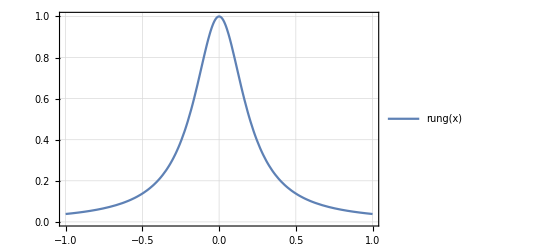

```mathematica
p1 = Plot[rung[x], {x, -1 ,1},PlotTheme->"Detailed"]
```

```mathematica
Per[i_, x_]:=Piecewise[{{Spl[i,x],  data⟦i+1⟧⟦1⟧< x<  data⟦i⟧⟦1⟧}}, 0];
Sup[x_] := Sum[Per[i,x],{i,1,Length[data]-1}];
```

```mathematica
p[i_]:=Plot[Per[i, x], {x, -1,  1}];
```

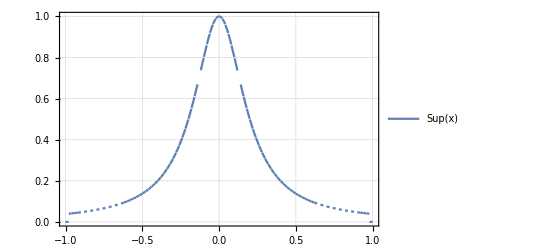

```mathematica
p2 = Plot[Sup[x], {x, -1, 1}, PlotTheme->"Detailed"]
```

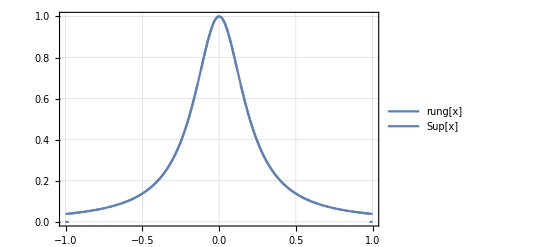

```mathematica
Show[p1, p2]
```